```mathematica
g[x_]:=1/2+1/(2x)(1-x^2/4)Log@Abs[(1+x/2)/(1-x/2)];
```

```mathematica
ϵ[x_,ξ_]:=1+(2ξ)/x^2*g[x];
ϵY[x_,ξ_]:=1+(2ξ)/x^2;
```

```mathematica
V[x_,ξ_]:=2/(2π)^2*1/(ϵ[x,ξ]*x^2)//Simplify;
```

```mathematica
Vspa[r_?NumericQ,ξ_]:=NIntegrate[Cos[q1 r]*qr*V[√(q1^2+qr^2),ξ],{qr,0,20},{q1,0,20}]
```

```mathematica
rs=Array[#&,30,{0,1.}];
Vs=Vspa[#,1]&/@rs
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{1.07583,1.03166,0.90928,0.736005,0.548244,0.38104,0.258747,0.189727,0.166505,0.170824,0.181434,0.181675,0.164279,0.132047,0.0947229,0.0637165,0.0469864,0.0460407,0.0559851,0.0682379,0.0745007,0.070209,0.0560732,0.0372433,0.0206609,0.0118787,0.0127453,0.0208755,0.0309948,0.0374411}

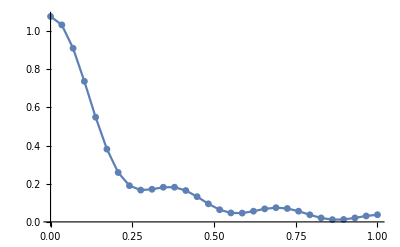

```mathematica
p1=ListLinePlot[Transpose@{rs,Vs},PlotMarkers->{Automatic, 7}]
```

```mathematica
p2=Plot[Exp[-r]/(4π r),{r,0.,1},PlotStyle->Orange,PlotRange->All];
```

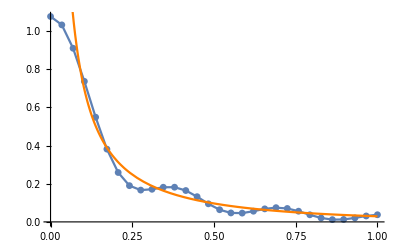

```mathematica
Show[p1,p2]
```